# Solving Polynomial Systems and ODE solvers

A polynomial system of n polynomials in n variables like
	p(z)=0
where p:ℂ^n→ℂ^n can have lots of solutions.  Some polynomial systems e.g.
	z_1^r_1=1, z_2^r_2=1,…,z_n^r_n=1 
have easily computed analytical solutions  
	z_(i,k)=cos(2π k/n_i)+ⅈ sin(2π k/n_i)  for k=0,1,2,…,r_i-1
for a potentially huge total of 
	m=∏_(i=1)^n r_i 
distinct solutions. Although analytical techniques provide a lot of information (including a way to compute the expected number of solutions) they do not provide practical solution techniques for large systems of interest. 

Polynomial homotopy (using a homotopy to connect a polynomial system with simple known solutions to the polynomial system of interest) is the current state of the art technique to compute all solutions of a large polynomial system.  https://bertini.nd.edu/ is the current state of the art polynomial homotopy package.  

Homotopy paths could be tracked using standard ODE solvers.  Bertini currently tracks paths using standard ODE solvers as predictors and Newton’s method as a corrector.  I believe that ODE based predictors designed for homotopy tracking could be a lot better than the standard predictors currently implemented.

## Homotopy

A polynomial homotopy h:ℂ^n×ℂ→ℂ^n for a polynomial p:ℂ^n→ℂ^n is a smooth function with h(z,0)=p(z) 
and h(z,1) a simple polynomial system with the same number of roots as p(z)=0.   Differentiating the homotopy condition
	h(z,a)=0	
gives the homotopy ODE
	∇h(z,a).z'(t)+∂_a h(z,a)a'[t]=0.
If we numerically solve this ODE along a specific path a=1 to a=0 in ℂ then each of the m known solutions of 
	h(z,1)=0
gives a numerical solutions of our target system
	 h(z,0)=p(z)=0.
We are going to call our input parameter t and in practice, homotopies have the form 
	γ(1-t)g(z)+t p(z)=0
with γ∈ℂ satisfying|γ|=1.

```mathematica
Clear[p,h,a,z,t,z1,z2]
p[{z1_,z2_}]:= {z2-2 z1^2+z2^2,2-2 z2-z1+2 z1^2}
γ=Normalize[1+4 ⅈ];
h[z_,t_]:= γ(1-t)p[z]+ t{z⟦1⟧^2-1,z⟦2⟧^2-1}
Dzh[{z1_,z2_},t_]=D[h[{z1,z2},t],{{z1,z2}}];
Dah[{z1_,z2_},t_]=D[h[{z1,z2},t],t];
StartPts=NSolveValues[h[{z1,z2},1]=={0,0},{z1,z2}];
Do[
zSol[i]=NDSolveValue[{
z'[t]==LinearSolve[Dzh[z[t],t],-Dah[z[t],t]],
z[1]==StartPts⟦i⟧},
z,{t,1,0}],
{i,Length[StartPts]}]
HomotopyRoots=Sort[Table[zSol[i][0],{i,Length[StartPts]}]];
MmaRoots=Sort[NSolveValues[p[{z1,z2}]=={0,0},{z1,z2}]];
TableForm[{MmaRoots,HomotopyRoots},TableDirections->Row,TableHeadings->{{"NSolve","Homotopy"},Automatic}]
```

| NSolve | Homotopy
1 | -0.426227-1.12449 ⅈ | 0.130302+1.52082 ⅈ | -0.426227-1.12449 ⅈ | 0.130302+1.52082 ⅈ
2 | -0.426227+1.12449 ⅈ | 0.130302-1.52082 ⅈ | -0.426227+1.12449 ⅈ | 0.130302-1.52082 ⅈ
3 | 0.926227-0.724627 ⅈ | 0.869698-0.980025 ⅈ | 0.926227-0.724627 ⅈ | 0.869698-0.980025 ⅈ
4 | 0.926227+0.724627 ⅈ | 0.869698+0.980025 ⅈ | 0.926227+0.724627 ⅈ | 0.869698+0.980025 ⅈ

We can see the paths in ℂ^2.

```mathematica
TabView[Table[
Subscript[z, i]->ParametricPlot[
{ReIm[zSol[1][a]⟦i⟧],ReIm[zSol[2][a]⟦i⟧],ReIm[zSol[3][a]⟦i⟧],ReIm[zSol[4][a]]⟦i⟧},
{a,0,1},PlotRange->All,PlotLegends->Automatic],{i,2}],2]
```

12

## Ramification Points.

A system of two quadratics in two unknowns “should” have four solutions. Multiple solutions are called ramified and points with multiple solutions are called ramification points.  A simple example probably make this clearer.  Here is a computation of “all” ramification points for a system.

```mathematica
Clear[h,z,a,z1,z2]
h[z_,a_]:= {z2-2 z1^2+z2^2,2-2 z2-z1+2 z1^2}+ a{z1^2-1,z2^2-1}
Dzh[{z1_,z2_},a_]=D[h[{z1,z2},a],{{z1,z2}}];
z1z2aRamPts=NSolveValues[{h[{z1,z2},a]=={0,0},Det[Dzh[{z1,z2},a]]==0},{z1,z2,a}];
Print["Ramification Points"]
TableForm[z1z2aRamPts,TableHeadings->{Automatic,{"z_1","z_2","a"}}]
```

Ramification Points

| z_1 | z_2 | a
1 | -6.92002 | 10.8681 | -0.70833
2 | -1.19635 | 0.246327 | 5.92576
3 | 0.893204+2.27213 ⅈ | 2.32327-0.547706 ⅈ | 2.91998+0.119582 ⅈ
4 | 0.893204-2.27213 ⅈ | 2.32327+0.547706 ⅈ | 2.91998-0.119582 ⅈ
5 | 1.29849 | 0.44672 | 3.97311
6 | 0.268488 | 1.05085 | 2.1672
7 | 0.0579956+0.0417957 ⅈ | -1.33936+1.02622 ⅈ | -0.594381-1.73813 ⅈ
8 | 0.0579956-0.0417957 ⅈ | -1.33936-1.02622 ⅈ | -0.594381+1.73813 ⅈ
9 | 0.294428 | 0.654831 | 0.996656
10 | 0.128798+0.695397 ⅈ | 0.101491-0.0688511 ⅈ | 0.735386-0.210881 ⅈ
11 | 0.128798-0.695397 ⅈ | 0.101491+0.0688511 ⅈ | 0.735386+0.210881 ⅈ
12 | 2.08649 | 2.74875 | -0.47637

Here are the solutions at one of the ramification points

```mathematica
i=1;
a=z1z2aRamPts⟦1,3⟧;
Print[StringForm["a=``",a]]
TableForm[NSolveValues[h[{z1,z2},a],{z1,z2}],TableHeadings->{Automatic,{"z_1","z_2"}}]
```

a=-0.70833

| z_1 | z_2
1 | 37.0233 | 60.4255
2 | 1.32394 | 1.57096
3 | -6.92002 | 10.8681
4 | -6.92002 | 10.8681

Systems have fewer distinct solutions than expected at ramification points (where parameterized curves cross) and when highest powers in the polynomials cancel. Paths intersect at ramifications so the ODE 
	∇h(z,a).z'(a)+∂_a h(z,a)=0
has more than one solution at such points.  Since h is a polynomial this only happens when the gradient ∇h(z,a)∈ℂ^(n×n) is not invertible.  In ODE theory a matrix multiplying the highest unknown derivative is called a mass-matrix.  Solutions go to ∞ when  the polynomial order drops.

A ramification point satisfies 
	h(z^*,a^*)=0  and det(A(z^*,a^*))=0.
If we hit a ramification point we will have to stop.  In theory, if we pick random paths (in implementation we choose a random complex number called γ which determines a circular contour) we should never hit a ramification point.  The careful way to say this is that there is “probability zero” of hitting a ramification point.  In practice, we will sometimes get close enough to hitting a ramification point that we will need to be careful.

In practice, if we get near a ramification point we need to solve the ODE very carefully.  At a ramification point the mass matrix 
	A=∇h
is singular so σ_n=0. Near a ramification point σ_n is small and and the condition number
	κ(A)=σ_max/σ_min=σ_1/σ_n 
is large.

We need z'', z''' etc for a Tylor or Pade scheme.   If we differentiate the ODE
	∇h(z,a).z'(a)=-∂_a h(z,a)≡RHS_1
using the chain rule and not worrying about dimensions etc. we get
	∇h(z,a).z''(a)+(∇_2 h(z,a).z'(a)+∂_a ∇h(z,a)).z'(a)=-∂_aa h(z,a)-∂_a ∇h(z,a).z'(a)
which is 
	∇h(z,a).z''(a)=-(∇_2 h(z,a).z'(a)+2∂_a ∇h(z,a).z'(a)+∂_aa h(z,a))
with a computable Right Hand Side 
	RHS_2≡-(∇_2 h(z,a).z'(a)+2∂_a ∇h(z,a).z'(a)+∂_aa h(z,a))
So we have another linear equation 
	A.z''=RHS_2	
with the same matrix A=∇h(z,a).  This process can be continued indefinitely to get
 	A.z^(k)=RHS_k
 This means that we can compute as many derivatives as we want from the ODE using a single matrix factorization.  This suggests that a Taylor series method for the homotopy predictor may have serious advantages over the explicit RK schemes used in Bertini.

## LU and QR and SVD Decompositions for A∈ℂ^(n×n)

An LU decompositions is a permutation matrix P,  unit lower triangular matrix L, and upper triangular matrix U satisfying 
	P.A=L.U
A QR decomposition is a permutation matrix P,  orthogonal matrix Q, and upper triangular matrix R satisfying 
	A.P=Q.R
An SVD is a pair of orthogonal matrices U and V with a real diagonal matrix Σ=diag(σ_1,σ_2,…,σ_n) satisfying σ_1≥σ_2≥…≥σ_n≥0
	A=U.Σ.Vᵀ
Solving A.x_1=b_1,…,A.x_k=b_k with takes O(n^3+k n^2) if you precompute one of these decompositions.  If you proceed naively it takes O(k n^3).

LU decompositions usually throw warnings if they detect that a matrix is probably badly conditioned. QR decomposition will produce upper triangular matrices R with small diagonal entries with badly conditioned input: the small entries are are usually near the bottom of R.  Pivoted QR decompositions which interchange columns ensure the diagonal of R is non-increasing in magnitude i.e.  |R_(j,j)|≥|R_(j+1,j+1)|:  the smallest entries are always at the bottom. The SVD computes the 2-norm condition number κ_2(A)=σ_1/σ_n: if σ_n=0 and σ_(n-1)>0 then null(A) is the span of the input singular vector in V matching v_n.

Condition number estimates are important because if κ(A)≈10^p then every time you compute with A you lose about p decimal places.  In double precision you start with 15.9≈16 decimal places.

If k(A)≈10^3 then z' from
	A.z'=RHS_1  
has about 13=16-3 decimal places. Since RHS_2 involves z' the z'' we get from
	A.z''=RHS_2
has about 13-3=10 decimal places. Since RHS_3 involves z'' the z''' we get from
	A.z'''=RHS_3
has about 10-3=7 decimal places.  This can not go on for ever because we are about to run out of decimal places.

There are ways to fix this problem (without computing everything in high precision) provided the condition number is not too large.  The obvious things to do are iterative improvement (see p139 section 3.5.3 in GvL 4th Edition) and/or to construct the critical low rank portion of the matrix in high precision.  As always fixing problems is more work.

```mathematica
RandomSparseComplex[n_,r_]:=Module[{dia=RandomComplex[{0,1+I},m],A,i,j,k=r*n},
A=SparseArray[Band[{1,1}]->dia,{n,n}];
Do[{i,j}=RandomInteger[{1,n},2];A⟦i,j⟧+=RandomComplex[{-1-I,1+I}],{k}];
A]

nList={20,50,100,200,400,800,1600};
TimingDataReal=Table[
A= RandomReal[{-1,1},{n,n}];
{n, 
AbsoluteTiming[LUDecomposition[A];]⟦1⟧,
AbsoluteTiming[QRDecomposition[A];]⟦1⟧,
AbsoluteTiming[QRDecomposition[A,Pivoting->True];]⟦1⟧,
AbsoluteTiming[SingularValueDecomposition[A];]⟦1⟧},
{n, nList}]
TimingDataComplex=Table[
A= RandomComplex[{-1-I,1+I},{n,n}];
{n, 
AbsoluteTiming[LUDecomposition[A];]⟦1⟧,
AbsoluteTiming[QRDecomposition[A];]⟦1⟧,
AbsoluteTiming[QRDecomposition[A,Pivoting->True];]⟦1⟧,
AbsoluteTiming[SingularValueDecomposition[A];]⟦1⟧},
{n, nList}]
TimingDataComplexSparse=Quiet[Table[
A= RandomSparseComplex[n,10];
{n, 
AbsoluteTiming[LUDecomposition[A];]⟦1⟧,
AbsoluteTiming[QRDecomposition[A];]⟦1⟧,
AbsoluteTiming[QRDecomposition[A,Pivoting->True];]⟦1⟧,
AbsoluteTiming[SingularValueDecomposition[A];]⟦1⟧},
{n, nList}]]
```

{{20,0.0000613,0.000025,0.0000251,0.0000767},{50,0.0000565,0.000209,0.0000911,0.000355},{100,0.0001393,0.0003123,0.0004455,0.0012395},{200,0.000517,0.002003,0.0021323,0.0051796},{400,0.0016232,0.0046257,0.0070213,0.0204082},{800,0.0063464,0.0210237,0.034731,0.090879},{1600,0.0437425,0.154091,0.421801,1.15968}}

{{20,0.0000989,0.000043,0.0000436,0.0001345},{50,0.0001054,0.0002304,0.0002167,0.0004911},{100,0.0002308,0.0005371,0.0007853,0.0017082},{200,0.0007874,0.0022526,0.0035412,0.0073878},{400,0.0061965,0.0138835,0.0218972,0.0361778},{800,0.0175769,0.0741891,0.114302,0.210406},{1600,0.142865,0.51625,1.4294,3.62984}}

{{20,0.000087,0.0000365,0.0000376,0.000122},{50,0.0001063,0.0002045,0.0002089,0.0004735},{100,0.0002795,0.0006899,0.0010987,0.0018298},{200,0.0010362,0.0021548,0.0035236,0.0062709},{400,0.0041619,0.0119124,0.0203616,0.0353849},{800,0.0262801,0.061973,0.112396,0.211703},{1600,0.149983,0.533871,1.40687,3.58723}}

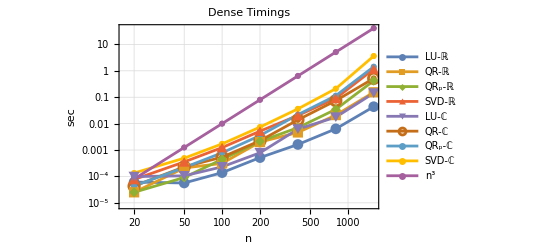

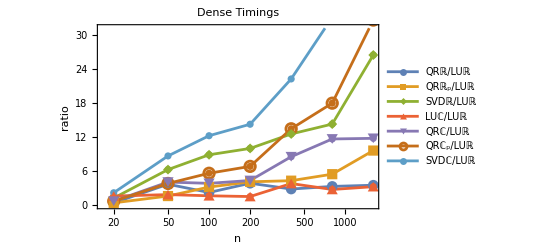

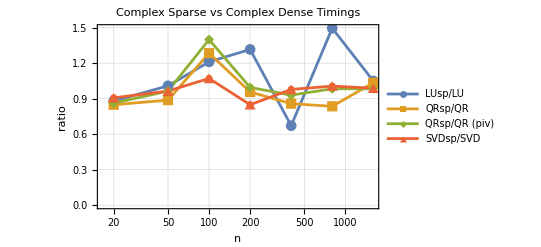

```mathematica
ListLogLogPlot[{
TimingDataReal⟦All,{1,2}⟧,
TimingDataReal⟦All,{1,3}⟧,
TimingDataReal⟦All,{1,4}⟧,
TimingDataReal⟦All,{1,5}⟧,
TimingDataComplex⟦All,{1,2}⟧,
TimingDataComplex⟦All,{1,3}⟧,
TimingDataComplex⟦All,{1,4}⟧,
TimingDataComplex⟦All,{1,5}⟧,
{nList,10^-8 nList^3}ᵀ
},GridLines->Automatic,FrameLabel->{"n","sec"},Frame->True,Joined->True,Mesh->All,
PlotMarkers->Automatic,PlotLabel->"Dense Timings",
PlotLegends->{"LU-ℝ","QR-ℝ", "QR_p-ℝ","SVD-ℝ","LU-ℂ","QR-ℂ","QR_p-ℂ","SVD-ℂ","n^3"}]
ListLogLinearPlot[{
{nList,TimingDataReal⟦All,3⟧/TimingDataReal⟦All,2⟧}ᵀ,
{nList,TimingDataReal⟦All,4⟧/TimingDataReal⟦All,2⟧}ᵀ,
{nList,TimingDataReal⟦All,5⟧/TimingDataReal⟦All,2⟧}ᵀ,
{nList,TimingDataComplex⟦All,2⟧/TimingDataReal⟦All,2⟧}ᵀ,
{nList,TimingDataComplex⟦All,3⟧/TimingDataReal⟦All,2⟧}ᵀ,
{nList,TimingDataComplex⟦All,4⟧/TimingDataReal⟦All,2⟧}ᵀ,
{nList,TimingDataComplex⟦All,5⟧/TimingDataReal⟦All,2⟧}ᵀ
},
GridLines->Automatic,FrameLabel->{"n","ratio"},Frame->True,Joined->True,Mesh->All,
PlotMarkers->Automatic,PlotLabel->"Dense Timings",
PlotLegends->{"QRℝ/LUℝ","QRℝ_p/LUℝ","SVDℝ/LUℝ","LUℂ/LUℝ","QRℂ/LUℝ","QRℂ_p/LUℝ","SVDℂ/LUℝ"}
]
ListLogLinearPlot[{
{nList,TimingDataComplexSparse⟦All,2⟧/TimingDataComplex⟦All,2⟧}ᵀ,
{nList,TimingDataComplexSparse⟦All,3⟧/TimingDataComplex⟦All,3⟧}ᵀ,
{nList,TimingDataComplexSparse⟦All,4⟧/TimingDataComplex⟦All,4⟧}ᵀ,
{nList,TimingDataComplexSparse⟦All,5⟧/TimingDataComplex⟦All,5⟧}ᵀ
},
GridLines->Automatic,FrameLabel->{"n","ratio"},Frame->True,Joined->True,Mesh->All,
PlotMarkers->Automatic,PlotLabel->"Complex Sparse vs Complex Dense Timings",
PlotLegends->{"LUsp/LU","QRsp/QR", "QRsp/QR (piv)","SVDsp/SVD"}
]
```

With a decomposition available the solution of A.x=b is cheap e.g. 
	A.x=b ⟹ L.U.x=Pᵀ.b⇒x=U^-1.L^-1.Pᵀ.x 
Notes: 
1) Applying the permutation matrix involves NO arithmetic. It just rearranges the entries.
2) You do not construct L^-1 you just do back substitution with L.  This takes O(n^2) operations.
3) You do not construct U^-1 you just do back substitution with U.  This takes O(n^2) operations.
4) If you have k right hand side vectors B=[b_1|b_2|…|b_k] and want to solve A.X=B then computers will organize the operations very efficiently as a BLAS-3 operation. On some computers you can solve 8 or more right hand sides in the same time as it takes to solve one.  
5) Ignoring all complicating factors solving A.X=B with an LU decomposition available is O(k n^2)

The same conclusion holds with QR and SVD decompositions
	A.X=B ⟹ Q.R.Pᵀ.X=B ⟹ x=P.R^-1.Q^H.X 
	A.X=B ⟹ U.Σ.V^H.X=B ⟹ x=V.Σ^-1.U^H.X 
Notes:
1) You do not construct R^-1 you just do back substitution with R.  This takes O(k n^2) operations.
2) You do not construct Σ^-1 it is simply a scaling by 1/σ_i.  This takes O(k n) operations.
3) Ignoring all complicating factors solving A.X=B with a QR or SVD decomposition available is O(k n^2).

In practice for badly conditioned problems: A QR decomposition (particularly with column pivoting) is more reliable than an LU decomposition and an SVD is more reliable than a QR decomposition.

## Bertini’s Solution and Variable Precision

Bertini automatically switches to variable-precision to compute accurate solutions near ramification points. It may not be clear but non-machine precision arithmetic is much much slower than double precision arithmetic.  In Mathematica high precision can easily use five times as much memory and slow down a thousand-fold. Five is worth worrying about but a thousand is worth obsessing over!

```mathematica
m=200;
AHigh=RandomReal[{-1,1},{m,m},WorkingPrecision->100];
ADouble=N[AHigh];
{tHigh,sHigh}={AbsoluteTiming[LUDecomposition[AHigh];]⟦1⟧,ByteCount[AHigh]};
{tNorm,sNorm}={AbsoluteTiming[LUDecomposition[ADouble];]⟦1⟧,ByteCount[ADouble]};
{1.0*sHigh/sNorm,tHigh/tNorm}
```

{5.26901,1121.46}

## Proposed Project and Solution

Think a little bit about improving the traditional ODE predictors implemented in Bertini.  There is an article (published in a very respectable journal) from the Bertini developers on our GitHub repository.   This article tests the different ODE predictors incorporated in Bertini.

The matrix decomposition in the function evaluation is expensive.  Minimize the number of matrix decompositions.  Is it worthwhile to use a QR rather than an LU?  Is it worthwhile to pivot in the QR decomposition?

Polynomials have cheap derivatives.  Use higher derivatives in the predictor.

The corrector Newton step uses the matrix decomposition.  Leverage “First Same As Last” ideas.

Try to avoid or reduce the use of high precision near ramification points

The discontinuity form at a generic ramification point is computable.   Use ODE tools that are “singularity” friendly.

The discontinuity form at a generic ramification point is computable. Use a suitable local change of variables to expand the volume around the ramification point to reduce the condition number.

Use standard numerical linear algebra tricks to maintain appropriate accuracy despite poor conditioning.

One possibility is iterative refinement.

Another possibility is to use higher precision in only a small part of the decomposition. The goal here would be only a rank-one piece of the decomposition in higher precision.